```mathematica
(* sove boundary problem for magnetic *)
(* shielding by spherical shell        *)
(* ----------------------------------- *)
```

```mathematica
(* phi1 = phi(b<r)    *)
(* phi2 = phi(a<r<b)  *)
(* phi3 = phi(r<a)    *)
```

```mathematica
phi1=-H0*r*Cos[th]+alpha/r^2*Cos[th]
phi2=beta*r*Cos[th]+gamma/r^2*Cos[th]
phi3=delta*r*Cos[th]
```

(alpha Cos[th])/r^2-H0 r Cos[th]

(gamma Cos[th])/r^2+beta r Cos[th]

delta r Cos[th]

```mathematica
(* bc at outer radius *)
(* ------------------- *)
eq1=(D[phi1,Cos[th]]==D[phi2,Cos[th]])/.r->b
```

alpha/b^2-b H0==b beta+gamma/b^2

```mathematica
eq2=(mu0*D[phi1,r]==mu*D[phi2,r])/.r->b
```

mu0 (-(2 alpha Cos[th])/b^3-H0 Cos[th])==mu (beta Cos[th]-(2 gamma Cos[th])/b^3)

```mathematica
(* bc at inner radius *)
(* ------------------- *)
```

```mathematica
eq3=(D[phi2,Cos[th]]==D[phi3,Cos[th]])/.r->a
```

a beta+gamma/a^2==a delta

```mathematica
eq4=(mu*D[phi2,r]==mu0*D[phi3,r])/.r->a
```

mu (beta Cos[th]-(2 gamma Cos[th])/a^3)==delta mu0 Cos[th]

```mathematica
(* solve bc's *)
(* ----------- *)
sol=Simplify[Solve[{eq1,eq2,eq3,eq4},{alpha,beta,gamma,delta}]]
```

{{alpha→(b^3 (-a^3+b^3) H0 (2 mu^2-mu mu0-mu0^2))/(-2 a^3 (mu-mu0)^2+b^3 (2 mu^2+5 mu mu0+2 mu0^2)),beta→(3 b^3 H0 mu0 (2 mu+mu0))/(2 a^3 (mu-mu0)^2-b^3 (2 mu^2+5 mu mu0+2 mu0^2)),gamma→(3 a^3 b^3 H0 (mu-mu0) mu0)/(2 a^3 (mu-mu0)^2-b^3 (2 mu^2+5 mu mu0+2 mu0^2)),delta→(9 b^3 H0 mu mu0)/(2 a^3 (mu-mu0)^2-b^3 (2 mu^2+5 mu mu0+2 mu0^2))}}

```mathematica
(* asymptotics as mu->infinity of outer field *)
(* ------------------------------------------- *)
alpha0=alpha/.sol[[1]]
```

(b^3 (-a^3+b^3) H0 (2 mu^2-mu mu0-mu0^2))/(-2 a^3 (mu-mu0)^2+b^3 (2 mu^2+5 mu mu0+2 mu0^2))

```mathematica
Series[alpha0,{mu,Infinity,0}]
```

b^3 H0+O[1/mu]^1

```mathematica
(* asymptotics as mu->infinity for inner field *)
(* -------------------------------------------- *)
delta0=delta/.sol[[1]]
```

(9 b^3 H0 mu mu0)/(2 a^3 (mu-mu0)^2-b^3 (2 mu^2+5 mu mu0+2 mu0^2))

```mathematica
Series[delta0,{mu,Infinity,1}]
```

(9 b^3 H0 mu0)/((2 a^3-2 b^3) mu)+O[1/mu]^2

```mathematica
(* numerical example *)
(* ------------------ *)
a0=2;
b0=3;
list={H0->1,mu0->1,mu->10,a->a0,b->b0}
```

{H0→1,mu0→1,mu→10,a→2,b→3}

```mathematica
alpha1=(alpha/.sol[[1]])/.list
beta1=(beta/.sol[[1]])/.list
gamma1=(gamma/.sol[[1]])/.list
delta1=(delta/.sol[[1]])/.list
```

1197/68

-21/68

-18/17

-15/34

```mathematica
phi[x_,y_]:=-1*x+alpha1*x/(x^2+y^2)^(3/2)/; Sqrt[x^2+y^2]>b0
phi[x_,y_]:=beta1*x+gamma1*x/(x^2+y^2)^(3/2)/;(Sqrt[x^2+y^2]>a0 && Sqrt[x^2+y^2]<b0)
phi[x_,y_]:=delta1*x/; Sqrt[x^2+y^2]<a0
```

```mathematica
M[x_,y_]:={D[phi[x1,y],x1]/.x1->1,D[phi[x,y2],y2]/.y2->y}
```

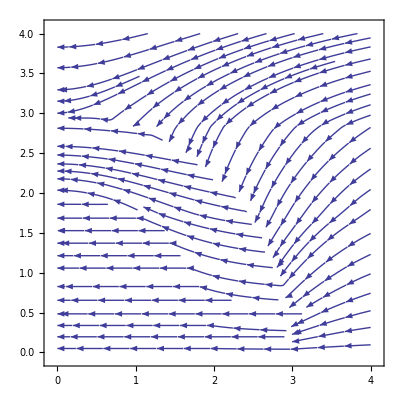

```mathematica
g1=StreamPlot[M[x,y],{x,0,4},{y,0,4}]
```

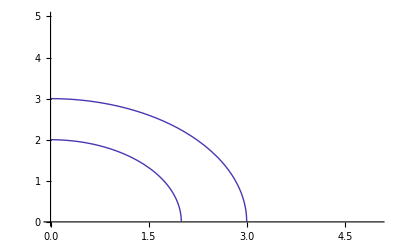

```mathematica
g2=Plot[{Sqrt[3^2-x^2],Sqrt[2^2-x^2]},{x,0,5},PlotStyle->{{Hue[0.7,0.7,0.7],Thick}},PlotRange->{0,5}]
```

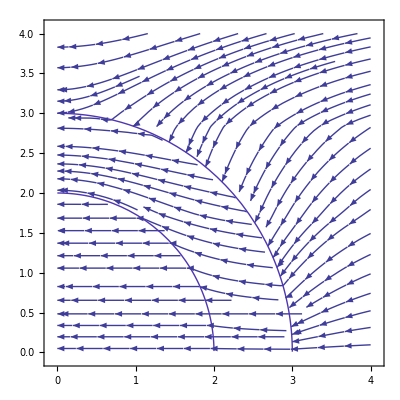

```mathematica
Show[g1,g2]
```